```mathematica
Subscript[q, 1]=I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1]
Subscript[q, 2]=(I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/(-Subscript[f, 1])+1)
Solve[((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/(-Subscript[f, 1])+1)+d)/(((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/(-Subscript[f, 1])+1)+d)/(-Subscript[f, 2])+1)=I(3.14*((2*10^-3)^2)/(628*10^-9))+Subscript[d, 2]&&Subscript[d, 1]+Subscript[d, 2]=0.07,{Subscript[f, 1],Subscript[f, 2]}]
```

```mathematica
Solve[((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/-f+1)+d+dd)/(((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/-f+1)+d+dd)/F+1)=I(3.14*((2*10^-3)^2)/(628*10^-9))+dd&&d+dd=0.07,{f,F}]
```

Set::write: Tag And in (ⅈ (3.14 (2 Power[«2»])^2))/(628 Power[«2»])+dd&&d+dd is Protected.

Set::write: Tag Times in (d+dd+((0.+5. ⅈ)-d)/(1-((0.+«18» ⅈ)+Times[«1»])/f))/(1+(d+dd+((0.+«18» ⅈ)+Times[«1»])/Plus[«2»])/F) is Protected.

Solve::naqs: 0.07 is not a quantified system of equations and inequalities.

Solve[0.07,{f,F}]

```mathematica
((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/-f+1)+d+dd)/(((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/-f+1)+d+dd)/F+1)
```

(d+dd+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f))/(1+(d+dd+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f))/F)

```mathematica
Simplify[(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/(1+(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/F)]
```

((d^2+d ((0.-5. ⅈ)+dd)+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)) F)/(d^2+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)-(0.+5. ⅈ) F+f F+d ((0.-5. ⅈ)+dd+F))

```mathematica
I(3.14*((2*10^-3)^2)/(628*10^-9))+dd
```

(0.+20. ⅈ)+dd

```mathematica
Im[((d^2+d ((0.-5.000000000000001 ⅈ)+dd)+(0.+5.000000000000001 ⅈ) f+dd ((0.-5.000000000000001 ⅈ)+f)) F)/(d^2+(0.+5.000000000000001 ⅈ) f+dd ((0.-5.000000000000001 ⅈ)+f)-(0.+5.000000000000001 ⅈ) F+f F+d ((0.-5.000000000000001 ⅈ)+dd+F))]
```

Im[((d^2+d ((0.-5. ⅈ)+dd)+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)) F)/(d^2+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)-(0.+5. ⅈ) F+f F+d ((0.-5. ⅈ)+dd+F))]

```mathematica
ComplexExpand[%6]
```

0.+(5. f^2 F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)

```mathematica
Simplify[0.+(5.000000000000001 f^2 F^2)/((0.-5.000000000000001 d-5.000000000000001 dd+5.000000000000001 f-5.000000000000001 F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)]
```

```mathematica
(5 f^2 F^2)/((0-5 d-5dd+5 f-5 F)^2+(0.+d^2+dd*f+f F+d (dd+F))^2)=3.14*((2*10^-3)^2)/(628*10^-9)
```

```mathematica
Subscript[q, 1]=I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1]
Subscript[q, 2]=(I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/((I(3.14((1*10^-3)^2)/(628*10^-9))-Subscript[d, 1])/(-Subscript[f, 1])+1)+d
Subscript[q, 3]=((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/(-Subscript[f, 1])+1)+0.07)/(((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14((1*10^-3)^2)/(628*10^-9))-d)/(-Subscript[f, 1])+1)+0.07)/(-Subscript[f, 2])+1)=I(3.14((2*10^-3)^2)/(628*10^-9))+(0.07-d)
```

```mathematica
((I(3.14*((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14*((1*10^-3)^2)/(628*10^-9))-d)/(-Subscript[f, 1])+1)+0.07)/(((I(3.14*((1*10^-3)^2)/(628*10^-9))-d)/((I(3.14*((1*10^-3)^2)/(628*10^-9))-d)/(-Subscript[f, 1])+1)+0.07)/(-Subscript[f, 2])+1)
```

(0.07+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f_1))/(1-(0.07+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f_1))/f_2)

```mathematica
Simplify[(0.07+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/Subscript[f, 1]))/(1-(0.07+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/Subscript[f, 1]))/Subscript[f, 2])]
```

-(1. ((0.+0.35 ⅈ)-0.07 d+((-0.07-5. ⅈ)+d) f_1) f_2)/((0.+0.35 ⅈ)-0.07 d+((0.-5. ⅈ)+d) f_2+f_1 ((-0.07-5. ⅈ)+d+f_2))

```mathematica
Cancel[%10]
```

-(1. ((0.+0.35 ⅈ)-0.07 d-(0.07+5. ⅈ) f_1+d f_1) f_2)/((0.+0.35 ⅈ)-0.07 d-(0.07+5. ⅈ) f_1+d f_1-(0.+5. ⅈ) f_2+d f_2+f_1 f_2)

```mathematica
Im[-(1. ((0.+0.35 ⅈ)-0.07 d-(0.07+5.000000000000001 ⅈ) f+d f) F)/((0.+0.3500000000000001 ⅈ)-0.07 d-(0.07+5.000000000000001 ⅈ) f+d f-(0.+5.000000000000001 ⅈ) F+d F+f F)]
```

-1. Im[(((0.+0.35 ⅈ)-0.07 d-(0.07+5. ⅈ) f+d f) F)/((0.+0.35 ⅈ)-0.07 d-(0.07+5. ⅈ) f+d f-(0.+5. ⅈ) F+d F+f F)]

```mathematica
(0.07+((5ⅈ)-d)/(1-((5 ⅈ)-d)/Subscript[f, 1]))/(1-(0.07+((5 ⅈ)-d)/(1-((5 ⅈ)-d)/Subscript[f, 1]))/Subscript[f, 2])
```

(0.07+(5 ⅈ-d)/(1-(5 ⅈ-d)/f_1))/(1-(0.07+(5 ⅈ-d)/(1-(5 ⅈ-d)/f_1))/f_2)

```mathematica
Simplify[(0.07+(5 ⅈ-d)/(1-(5 ⅈ-d)/Subscript[f, 1]))/(1-(0.07+(5 ⅈ-d)/(1-(5 ⅈ-d)/Subscript[f, 1]))/Subscript[f, 2])]
```

```mathematica
-(((0.35ⅈ)-0.07 d+((-0.07-5*ⅈ)+d) Subscript[f, 1]) Subscript[f, 2])/((0.35ⅈ)-0.07d+((-5 ⅈ)+d) Subscript[f, 2]+Subscript[f, 1] ((-0.07-5 ⅈ)+d+Subscript[f, 2]))
```

```mathematica
Im[-(((0.+0.35 ⅈ)-0.07 d+((-0.07-5. ⅈ)+d) Subscript[f, 1]) Subscript[f, 2])/((0.+0.35 ⅈ)-0.07 d+(-5 ⅈ+d) Subscript[f, 2]+Subscript[f, 1] ((-0.07-5. ⅈ)+d+Subscript[f, 2]))]
```

-Im[(((0.+0.35 ⅈ)-0.07 d+((-0.07-5. ⅈ)+d) f_1) f_2)/((0.+0.35 ⅈ)-0.07 d+(-5 ⅈ+d) f_2+f_1 ((-0.07-5. ⅈ)+d+f_2))]

```mathematica
ComplexExpand[-Im[(((0.+0.35 ⅈ)-0.07 d+((-0.07-5. ⅈ)+d) Subscript[f, 1]) Subscript[f, 2])/((0.+0.35 ⅈ)-0.07 d+(-5 ⅈ+d) Subscript[f, 2]+Subscript[f, 1] ((-0.07-5. ⅈ)+d+Subscript[f, 2]))]]
```

0.+(5.55112×10^-17 d f_2^2)/((0.35-5. f_1-5 f_2)^2+(0.-0.07 d+d f_2+f_1 (-0.07+d+f_2))^2)+(5.55112×10^-17 f_1 f_2^2)/((0.35-5. f_1-5 f_2)^2+(0.-0.07 d+d f_2+f_1 (-0.07+d+f_2))^2)+(5. f_1^2 f_2^2)/((0.35-5. f_1-5 f_2)^2+(0.-0.07 d+d f_2+f_1 (-0.07+d+f_2))^2)

```mathematica
FullSimplify[%19]
```

```mathematica
((5.551115123125783*^-17 d+Subscript[f, 1] (5.551115123125783*^-17+5. Subscript[f, 1])) Subscript[f, 2]^2)/(0.12249999999999998+0.004900000000000001 d^2+Subscript[f, 2] (-3.5-0.14 d^2+(25.+1. d^2) Subscript[f, 2])+Subscript[f, 1]^2 (25.0049+d (-0.14+1. d)+Subscript[f, 2] (-0.14+2. d+1. Subscript[f, 2]))+Subscript[f, 1] (-3.5+(0.009800000000000001-0.14 d) d+Subscript[f, 2] (50.+d (-0.28+2. d)+2. d Subscript[f, 2])))
```

```mathematica
(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/(1+(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/F)
```

(d+dd+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f))/(1+(d+dd+((0.+5. ⅈ)-d)/(1-((0.+5. ⅈ)-d)/f))/F)

```mathematica
Simplify[(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/(1+(d+dd+((0.+5.000000000000001 ⅈ)-d)/(1-((0.+5.000000000000001 ⅈ)-d)/f))/F)]
```

```mathematica
Re[((d^2+d ((0.-5.000000000000001 ⅈ)+dd)+(0.+5.000000000000001 ⅈ) f+dd ((0.-5.000000000000001 ⅈ)+f)) F)/(d^2+(0.+5.000000000000001 ⅈ) f+dd ((0.-5.000000000000001 ⅈ)+f)-(0.+5.000000000000001 ⅈ) F+f F+d ((0.-5.000000000000001 ⅈ)+dd+F))]
```

Re[((d^2+d ((0.-5. ⅈ)+dd)+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)) F)/(d^2+(0.+5. ⅈ) f+dd ((0.-5. ⅈ)+f)-(0.+5. ⅈ) F+f F+d ((0.-5. ⅈ)+dd+F))]

```mathematica
ComplexExpand[%23]
```

0.+(25. d^2 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(d^4 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(50. d dd F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(2 d^3 dd F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(25. dd^2 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(d^2 dd^2 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)-(50. d f F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)-(50. dd f F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(2 d^2 dd f F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(2 d dd^2 f F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(25. f^2 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(dd^2 f^2 F)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(25. d F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(d^3 F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(25. dd F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(d^2 dd F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)-(25. f F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(d^2 f F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(2 d dd f F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)+(dd f^2 F^2)/((0.-5. d-5. dd+5. f-5. F)^2+(0.+d^2+dd f+f F+d (0.+dd+F))^2)

```mathematica
Log[E,0.05]
```

-2.99573

```mathematica
(q/(q/-f+1)+d)/((q/(q/-f+1)+d)/-F+1)
```

(d+q/(1-q/f))/(1-(d+q/(1-q/f))/F)

```mathematica
Simplify[(d+q/(1-q/f))/(1-(d+q/(1-q/f))/F)]
```

```mathematica
F (d (f-q)+f q)=(Q f (F-q)-F q+d (-f+q))
```

F q-d (-f+q)+F (d (f-q)+f q)-f (F-q) Q

```mathematica
Simplify[F q-d (-f+q)+F (d (f-q)+f q)-f (F-q) Q]
```

d (1+F) (f-q)+f q Q+F (q+f q-f Q)

```mathematica
F (0.07(f-0.05 ⅈ)+f *0.05 ⅈ)=((0.2 ⅈ+0.07)f (F-0.05 ⅈ)-F *0.05 ⅈ+0.07 (-f+0.05 ⅈ))
```

```mathematica
I(3.14*((0.1*10^-3)^2)/(628*10^-9))
```

```mathematica
F (0.07(f-0.05 ⅈ)+f *0.05 ⅈ)
```

((0.+0.05 ⅈ) f+0.07 ((0.-0.05 ⅈ)+f)) F

```mathematica
Simplify[((0.+0.05 ⅈ) f+0.07 ((0.-0.05 ⅈ)+f)) F]
```

((0.-0.0035 ⅈ)+(0.07+0.05 ⅈ) f) F

```mathematica
((0.2 ⅈ+0.07)f (F-0.05 ⅈ)-F *0.05 ⅈ+0.07 (-f+0.05 ⅈ))
```

0.07 ((0.+0.05 ⅈ)-f)-(0.+0.05 ⅈ) F+(0.07+0.2 ⅈ) f ((0.-0.05 ⅈ)+F)

```mathematica
Simplify[0.07 ((0.+0.05 ⅈ)-f)-(0.+0.05 ⅈ) F+(0.07+0.2 ⅈ) f ((0.-0.05 ⅈ)+F)]
```

(-4.33681×10^-19+0.0035 ⅈ)+f ((-0.06-0.0035 ⅈ)+(0.07+0.2 ⅈ) F)-(3.46945×10^-18+0.05 ⅈ) F

```mathematica
((0.2 s+0.07)f (F-0.05s)-F *0.05s+0.07 (-f+0.05s))
```

0.07 (-f+0.05 s)+f (F-0.05 s) (0.07+0.2 s)-0.05 F s

```mathematica
Expand[0.07 (-f+0.05 s)+f (F-0.05 s) (0.07+0.2 s)-0.05 F s]
```

-0.07 f+0.07 f F+0.0035 s-0.0035 f s-0.05 F s+0.2 f F s-0.01 f s^2

```mathematica
F (0.07(f-0.05s)+f *0.05s)
```

F (0.07 (f-0.05 s)+0.05 f s)

```mathematica
Expand[F (0.07 (f-0.05 s)+0.05 f s)]
```

0.07 f F-0.0035 F s+0.05 f F s

```mathematica
(d+q/(1-q/f))/(1-(d+q/(1-q/f))/F)
```

(d+q/(1-q/f))/(1-(d+q/(1-q/f))/F)

```mathematica
Simplify[(d+q/(1-q/f))/(1-(d+q/(1-q/f))/F)]
```

```mathematica
F (d (f-q)+f q)=Q(f (F-q)-F q+d (-f+q))
```

```mathematica
0.2s( f (F-0.05s)-F *0.05s+d (-f+0.05s))
```

```mathematica
(0.2s+0.07)*(f (F-0.05 s)+d (-f+0.05 s)-0.05 F s)
```

(0.07+0.2 s) (f (F-0.05 s)+d (-f+0.05 s)-0.05 F s)

```mathematica
Expand[(0.07+0.2 s) (f (F-0.05 s)+d (-f+0.05 s)-0.05 F s)]
```

-0.07 d f+0.07 f F+0.0035 d s-0.0035 f s-0.2 d f s-0.0035 F s+0.2 f F s+0.01 d s^2-0.01 f s^2-0.01 F s^2

```mathematica
Expand[0.2 s (f (F-0.05 s)+d (-f+0.05 s)-0.05 F s)]
```

-0.2 d f s+0.2 f F s+0.01 d s^2-0.01 f s^2-0.01 F s^2

```mathematica
(0.07+0.2 s) (f (F-0.05 s)+0.07(-f+0.05 s)-0.05 F s)
```

(0.07+0.2 s) (f (F-0.05 s)+0.07 (-f+0.05 s)-0.05 F s)

```mathematica
Expand[(0.07+0.2 s) (f (F-0.05 s)+0.07 (-f+0.05 s)-0.05 F s)]
```

-0.0049 f+0.07 f F+0.000245 s-0.0175 f s-0.0035 F s+0.2 f F s+0.0007 s^2-0.01 f s^2-0.01 F s^2

```mathematica
-0.004900000000000001 f+0.07 f F+0.00024500000000000005 s-0.0175 f s-0.0035000000000000005 F s+0.2 f F s+0.0007000000000000001 *(-1)+0.010000000000000002 f +0.010000000000000002 F
```

-0.0007+0.0051 f+0.01 F+0.07 f F+0.000245 s-0.0175 f s-0.0035 F s+0.2 f F s

```mathematica
Simplify[-0.0007000000000000001+0.005100000000000001 f+0.010000000000000002 F+0.07 f F+0.00024500000000000005 s-0.0175 f s-0.0035000000000000005 F s+0.2 f F s]
```

-0.0007+f (0.0051+F (0.07+0.2 s)-0.0175 s)+F (0.01-0.0035 s)+0.000245 s

```mathematica
Expand[-0.0007000000000000001+f (0.005100000000000001+F (0.07+0.2 s)-0.0175 s)+F (0.010000000000000002-0.0035000000000000005 s)+0.00024500000000000005 s]
```

```mathematica
+0.00024500000000000005 s-0.0175 f s-0.0035000000000000005 F s+0.2 f F s
```

```mathematica
F (0.07 (f-0.05s)+f 0.05s)
```

F (0.07 (f-0.05 s)+0.05 f s)

```mathematica
Expand[F (0.07 (f-0.05 s)+0.05 f s)]
```

```mathematica
-0.0035000000000000005 F s+0.05 f F s
```

```mathematica
-0.0007+0.0051 f+0.01 F=0
```

```mathematica
+0.15 f F = 0.0175f-0.000245
```

```mathematica
Solve[-0.0007+0.0051 f+0.01 F==0&&+0.15 f F ==0.0175f-0.000245,{f,F}]
```

```mathematica
{{f->-0.11852406277392684,F->0.1304472720147027},{f->0.027020794800070632,F->0.05621939465196398}}*
```

```mathematica
(5*10^-6/6.28)^(1/2)
```

```mathematica
0.000892288262810312
```

```mathematica
√3*59
```

59 √3

```mathematica
N[59 √3]
```

```mathematica
(107/59)^2
```

11449/3481

```mathematica
N[11449/3481]
```

```mathematica
82.9*107/59
```

150.344

```mathematica
368/338
```

184/169

```mathematica
N[184/169]
```

```mathematica
1.0887573964497042^2
```

```mathematica
1.1853926683239382-1
```

0.185393

```mathematica
Rationalize[0.1853926683239382]
```

5295/28561

```mathematica
Rationalize[1.1853926683239382]
```

33856/28561

```mathematica
(60/150)^2
```

4/25

```mathematica
N[4/25]
```

0.16

```mathematica
N[9/25]
```

0.36

```mathematica
N[9/100]
```

0.09

```mathematica
0.3/(3.14((338*10^-6)^2)/(514*10^-9))
```

```mathematica
0.42985434906670866^2+1
```

1.18477

```mathematica
(0.5/(3.14*((8.92*10^-4)^2)/(5*10^-6)))^2+1
```

2.00129

```mathematica
353*2-338
```

368

```mathematica
2.0012932850893126*(8.92*10^-4)^2
```

1.59236×10^-6

```mathematica
1.5923570203873028*^-6
```

```mathematica
√(1.5923570203873028*^-6)+8.92*10^-4
```

```mathematica
0.002153886294555616/2
```

```mathematica
0.001076943147277808^2
```

1.15981×10^-6

```mathematica
4 Pi^2/((5*10^-6)^3)6.626*10^-34*3.0*10^8*10^-3/10^-3*1.15981*10^-6(2*((5*10^-6)^2)/(0.4*Pi*10^-3)*1.26*10^27*1.01*10^5/300*10^-9*10^-6-1)
```

```mathematica
1.854763779093139*^27 *6.626*10^-34
```

1.22897×10^-6

```mathematica
0.03*10^9*4 Pi^2/((5*10^-6)^3)6.626*10^-34*3.0*10^8*10^-3/10^-3*1.15981*10^-6(4*((5*10^-6)^2)/(0.4*Pi)*1.26*10^27*1.01*10^5/300*10^-9*10^-6-1)
```

0.0737358

```mathematica
1.2289664800271141*^-6*0.03
```

```mathematica
3.6868994400813425*^-8*10^9
```

36.869

```mathematica
10^9*4 Pi^2/((5*10^-6)^3)6.626*10^-34*3.0*10^8*1.15981*10^-6(√(4*((5*10^-6)^2)/(8*Pi)*1.26*10^27*1.01*10^5/300*10^-9*10^-6)-√0.02)^2
```

0.122052

```mathematica
√(2*((5*10^-6)^2)/(8*Pi*10^-3)*1.26*10^27*1.01*10^5/300*10^-9*10^-6*0.02)-0.02
```

129.897

```mathematica
√(5*10^-6/(2Pi))(1(2-1))^(1/2)
```

1/(200 √(10 π))

```mathematica
N[1/(200 √(10 π))]
```

0.000892062

```mathematica
ScientificForm[0.0008920620580763855]
```

8.92062×10^-4

```mathematica
0.03*10^9*4 Pi^2/((5*10^-6)^3)6.626*10^-34*3.0*10^8*1.15981*10^-6(√(2*((5*10^-6)^2)/(8*Pi*10^-3)*1.26*10^27*1.01*10^5/300*10^-9*10^-6)-√0.02)^2
```

1.84288

```mathematica
√(2*0.02*2*((5*10^-6)^2)/(8*Pi)*1.26*10^27*1.01*10^5/300*10^-9*10^-6)
```

5.81006

```mathematica
2*
```

```mathematica
50*(5*10^-6)^2/(2*3.14*1.3806505*10^-23*300)
```

4.80558×10^10

```mathematica
670/1.33
```

503.759

```mathematica
Log[10]/0.1 10^9*8*Pi*20*10^-9/(503.759*10^-9)^2
```

```mathematica
(4.560788234818439*10^10)*3*10^17/(1.33*514)
```

2.00146×10^25

```mathematica
8*Pi*6.626*10^-34*3*(10^17/(1.33*514))/(((514/1.33)*10^-9)^2 0.001)
```

0.04893

```mathematica
D[Log[E,Sinh[y]/y],y]
```

y Csch[y] (Cosh[y]/y-Sinh[y]/y^2)

```mathematica
Simplify[y Csch[y] (Cosh[y]/y-Sinh[y]/y^2)]
```

-1/y+Coth[y]

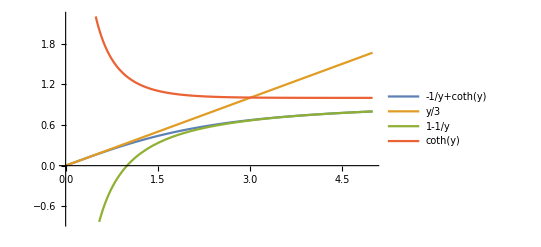

```mathematica
Plot[{-1/y+Coth[y],y/3,1-1/y,Coth[y]},{y,0,5},PlotLegends->"Expressions"]
```

```mathematica
-1/y+Coth[y]
```

```mathematica
Series[Coth[y]-1/y,{y,0,5}]
```

y/3-y^3/45+(2 y^5)/945+O[y]^6

```mathematica
Series[1/(4(1-x/L)^2),{x,0,5}]
Coth[y]-Cosh[y]/Sinh[y]
```

1/4+x/(2 L)+(3 x^2)/(4 L^2)+x^3/L^3+(5 x^4)/(4 L^4)+(3 x^5)/(2 L^5)+O[x]^6

0

```mathematica
D[Sinh[y]/y,y]
```

Cosh[y]/y-Sinh[y]/y^2

```mathematica
Sinh[x]
```

Sinh[x]

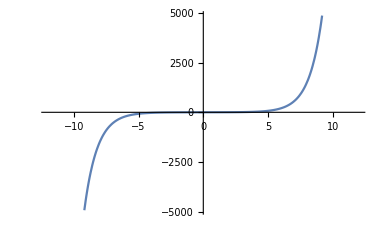

```mathematica
Plot[Sinh[x],{x,-12.,12.}]
```

```mathematica
k(x-R)^2
```

k (-R+x)^2

```mathematica
D[(k (-R+x)^2), x]
```

2 k (-R+x)

```mathematica
2 u/k/((5t)/(k+5t)+t/(k+t))
```

(2 u)/(k (t/(k+t)+(5 t)/(k+5 t)))

```mathematica
Simplify[(2 u)/(k (t/(k+t)+(5 t)/(k+5 t)))]
```

((k+t) (k+5 t) u)/(k t (3 k+5 t))

```mathematica
Expand[((k+t) (k+5 t) u)/(k t (3 k+5 t))]
```

(6 u)/(3 k+5 t)+(k u)/(t (3 k+5 t))+(5 t u)/(k (3 k+5 t))

```mathematica
((10t+t) (10t+5 t) u)/(10t*t (3 *10t+5 t))
```

(33 u)/(70 t)

```mathematica
-8200+22.2*300
```

-1540.